## Constants

```mathematica
Sites=6;
```

```mathematica
tmax=20;
```

```mathematica
Nt=128;
dt=tmax/Nt;
Length[ts=N@Range[0,tmax-dt,dt]];
```

```mathematica
times=Table[t,{t,0,tmax-dt,dt}];
```

```mathematica
Runs=1000000;
mSIM=10;
```

```mathematica
Uvalue=1;
μvalue=1;
Jvalue=0.01;
navgvalue=1;
```

```mathematica
putvalues:={U->Uvalue,J->Jvalue,navg->navgvalue,μ->μvalue};
```

## Dynamic Equations

```mathematica
vs=Table[Table[s[m,n][t],{n,1,3}],{m,1,Sites}];
ds=Table[Table[s[m,n]'[t],{n,1,3}],{m,1,Sites}];
initialss:=Flatten[Table[Table[s[m,n][0]==Subscript[s, 0][m,n],{n,1,3}],{m,1,Sites}]];
Δs[m_,ow_]:=Table[D[ow,s[m,n][t]],{n,1,3}];
```

```mathematica
sw[m_,ow_]:=vs[[m]]  ow-ⅈ/2 vs[[m]] ×Δs[m,ow]-1/8(Δs[m,ow]+Table[vs[[m]] .Δs[m,Δs[m,ow][[n]]],{n,1,3}]-1/2 vs[[m]]  Sum[Δs[m,Δs[m,ow][[n]]][[n]],{n,1,3}]);
swb[m_,ow_]:=vs[[m]]  ow+ⅈ/2 vs[[m]] ×Δs[m,ow]-1/8(Δs[m,ow]+Table[vs[[m]] .Δs[m,Δs[m,ow][[n]]],{n,1,3}]-1/2 vs[[m]]  Sum[Δs[m,Δs[m,ow][[n]]][[n]],{n,1,3}]);
```

```mathematica
Hs[m_,ow_]:=U/2 sw[m,sw[m,ow][[3]]][[3]]-J navg (sw[m,ow][[1]](Sum[sw[n,1][[1]],{n,1,m-1}]+Sum[sw[n,1][[1]],{n,m+1,Sites}])+sw[m,ow][[2]](Sum[sw[n,1][[2]],{n,1,m-1}]+Sum[sw[n,1][[2]],{n,m+1,Sites}]))-μ sw[m,ow][[3]];
Hsb[m_,ow_]:=U/2 swb[m,swb[m,ow][[3]]][[3]]-J navg (swb[m,ow][[1]](Sum[swb[n,1][[1]],{n,1,m-1}]+Sum[swb[n,1][[1]],{n,m+1,Sites}])+swb[m,ow][[2]](Sum[swb[n,1][[2]],{n,1,m-1}]+Sum[swb[n,1][[2]],{n,m+1,Sites}]))-μ swb[m,ow][[3]];
```

```mathematica
eqnss1=Table[ds[[1,n]]==Simplify[ⅈ (Hs[1,vs[[1,n]]]-Hsb[1,vs[[1,n]]])],{n,1,3}]
```

{s[1,1]'[t]==s[1,2][t] (μ-U s[1,3][t])-J navg s[1,3][t] (s[2,2][t]+s[3,2][t]+s[4,2][t]+s[5,2][t]+s[6,2][t]),s[1,2]'[t]==s[1,1][t] (-μ+U s[1,3][t])+J navg s[1,3][t] (s[2,1][t]+s[3,1][t]+s[4,1][t]+s[5,1][t]+s[6,1][t]),s[1,3]'[t]==J navg (-s[1,2][t] (s[2,1][t]+s[3,1][t]+s[4,1][t]+s[5,1][t]+s[6,1][t])+s[1,1][t] (s[2,2][t]+s[3,2][t]+s[4,2][t]+s[5,2][t]+s[6,2][t]))}

```mathematica
eqnss:=Flatten[Table[eqnss1/.Flatten[Table[{s[1,n]'[t]->s[m,n]'[t],s[1,n][t]->s[m,n][t],s[m,n][t]->s[1,n][t]},{n,1,3}]],{m,1,Sites}]];
```

```mathematica
MatrixForm[eqnss]
```

(s[1,1]'[t]==s[1,2][t] (μ-U s[1,3][t])-J navg s[1,3][t] (s[2,2][t]+s[3,2][t]+s[4,2][t]+s[5,2][t]+s[6,2][t])
s[1,2]'[t]==s[1,1][t] (-μ+U s[1,3][t])+J navg s[1,3][t] (s[2,1][t]+s[3,1][t]+s[4,1][t]+s[5,1][t]+s[6,1][t])
s[1,3]'[t]==J navg (-s[1,2][t] (s[2,1][t]+s[3,1][t]+s[4,1][t]+s[5,1][t]+s[6,1][t])+s[1,1][t] (s[2,2][t]+s[3,2][t]+s[4,2][t]+s[5,2][t]+s[6,2][t]))
s[2,1]'[t]==s[2,2][t] (μ-U s[2,3][t])-J navg s[2,3][t] (s[1,2][t]+s[3,2][t]+s[4,2][t]+s[5,2][t]+s[6,2][t])
s[2,2]'[t]==s[2,1][t] (-μ+U s[2,3][t])+J navg s[2,3][t] (s[1,1][t]+s[3,1][t]+s[4,1][t]+s[5,1][t]+s[6,1][t])
s[2,3]'[t]==J navg (-s[2,2][t] (s[1,1][t]+s[3,1][t]+s[4,1][t]+s[5,1][t]+s[6,1][t])+s[2,1][t] (s[1,2][t]+s[3,2][t]+s[4,2][t]+s[5,2][t]+s[6,2][t]))
s[3,1]'[t]==s[3,2][t] (μ-U s[3,3][t])-J navg s[3,3][t] (s[1,2][t]+s[2,2][t]+s[4,2][t]+s[5,2][t]+s[6,2][t])
s[3,2]'[t]==s[3,1][t] (-μ+U s[3,3][t])+J navg s[3,3][t] (s[1,1][t]+s[2,1][t]+s[4,1][t]+s[5,1][t]+s[6,1][t])
s[3,3]'[t]==J navg (-s[3,2][t] (s[1,1][t]+s[2,1][t]+s[4,1][t]+s[5,1][t]+s[6,1][t])+s[3,1][t] (s[1,2][t]+s[2,2][t]+s[4,2][t]+s[5,2][t]+s[6,2][t]))
s[4,1]'[t]==s[4,2][t] (μ-U s[4,3][t])-J navg s[4,3][t] (s[1,2][t]+s[2,2][t]+s[3,2][t]+s[5,2][t]+s[6,2][t])
s[4,2]'[t]==s[4,1][t] (-μ+U s[4,3][t])+J navg s[4,3][t] (s[1,1][t]+s[2,1][t]+s[3,1][t]+s[5,1][t]+s[6,1][t])
s[4,3]'[t]==J navg (-s[4,2][t] (s[1,1][t]+s[2,1][t]+s[3,1][t]+s[5,1][t]+s[6,1][t])+s[4,1][t] (s[1,2][t]+s[2,2][t]+s[3,2][t]+s[5,2][t]+s[6,2][t]))
s[5,1]'[t]==s[5,2][t] (μ-U s[5,3][t])-J navg s[5,3][t] (s[1,2][t]+s[2,2][t]+s[3,2][t]+s[4,2][t]+s[6,2][t])
s[5,2]'[t]==s[5,1][t] (-μ+U s[5,3][t])+J navg s[5,3][t] (s[1,1][t]+s[2,1][t]+s[3,1][t]+s[4,1][t]+s[6,1][t])
s[5,3]'[t]==J navg (-s[5,2][t] (s[1,1][t]+s[2,1][t]+s[3,1][t]+s[4,1][t]+s[6,1][t])+s[5,1][t] (s[1,2][t]+s[2,2][t]+s[3,2][t]+s[4,2][t]+s[6,2][t]))
s[6,1]'[t]==-J navg (s[1,2][t]+s[2,2][t]+s[3,2][t]+s[4,2][t]+s[5,2][t]) s[6,3][t]+s[6,2][t] (μ-U s[6,3][t])
s[6,2]'[t]==J navg (s[1,1][t]+s[2,1][t]+s[3,1][t]+s[4,1][t]+s[5,1][t]) s[6,3][t]+s[6,1][t] (-μ+U s[6,3][t])
s[6,3]'[t]==J navg ((s[1,2][t]+s[2,2][t]+s[3,2][t]+s[4,2][t]+s[5,2][t]) s[6,1][t]-(s[1,1][t]+s[2,1][t]+s[3,1][t]+s[4,1][t]+s[5,1][t]) s[6,2][t]))

## Delta functions

```mathematica
szup3={1,0,0};
szmiddle3={0,0,0};
szdown3={0,0,-1};
```

```mathematica
inits3=Table[0,{Sites},{3}];
```

```mathematica
inits3={szup3,szmiddle3,szdown3,szup3,szmiddle3,szdown3};
```

```mathematica
(*inits=Table[RandomVariate[NormalDistribution[meansz0[[n]],√(varsz0[[n]]+1/8)]],{Sites},{n,1,8}];*)
```

```mathematica
ssolve=NDSolve[(eqnss~Join~initialss)/.{U->Uvalue,μ->μvalue,J->Jvalue,navg->navgvalue}~Join~Flatten[Table[Subscript[s, 0][m,n]->inits3[[m,n]],{m,1,Sites},{n,1,3}]],Flatten[vs],{t,0,tmax},MaxSteps->∞];
```

```mathematica
(*DSolve[(eqnss~Join~initialss),Flatten[vs],t]*)
```

DSolve[{s[1,1]'[t]==s[1,2][t] (μ-U s[1,3][t])-J navg s[1,3][t] (s[2,2][t]+s[3,2][t]+s[4,2][t]+s[5,2][t]+s[6,2][t]),s[1,2]'[t]==s[1,1][t] (-μ+U s[1,3][t])+J navg s[1,3][t] (s[2,1][t]+s[3,1][t]+s[4,1][t]+s[5,1][t]+s[6,1][t]),s[1,3]'[t]==J navg (-s[1,2][t] (s[2,1][t]+s[3,1][t]+s[4,1][t]+s[5,1][t]+s[6,1][t])+s[1,1][t] (s[2,2][t]+s[3,2][t]+s[4,2][t]+s[5,2][t]+s[6,2][t])),s[2,1]'[t]==s[2,2][t] (μ-U s[2,3][t])-J navg s[2,3][t] (s[1,2][t]+s[3,2][t]+s[4,2][t]+s[5,2][t]+s[6,2][t]),s[2,2]'[t]==s[2,1][t] (-μ+U s[2,3][t])+J navg s[2,3][t] (s[1,1][t]+s[3,1][t]+s[4,1][t]+s[5,1][t]+s[6,1][t]),s[2,3]'[t]==J navg (-s[2,2][t] (s[1,1][t]+s[3,1][t]+s[4,1][t]+s[5,1][t]+s[6,1][t])+s[2,1][t] (s[1,2][t]+s[3,2][t]+s[4,2][t]+s[5,2][t]+s[6,2][t])),s[3,1]'[t]==s[3,2][t] (μ-U s[3,3][t])-J navg s[3,3][t] (s[1,2][t]+s[2,2][t]+s[4,2][t]+s[5,2][t]+s[6,2][t]),s[3,2]'[t]==s[3,1][t] (-μ+U s[3,3][t])+J navg s[3,3][t] (s[1,1][t]+s[2,1][t]+s[4,1][t]+s[5,1][t]+s[6,1][t]),s[3,3]'[t]==J navg (-s[3,2][t] (s[1,1][t]+s[2,1][t]+s[4,1][t]+s[5,1][t]+s[6,1][t])+s[3,1][t] (s[1,2][t]+s[2,2][t]+s[4,2][t]+s[5,2][t]+s[6,2][t])),s[4,1]'[t]==s[4,2][t] (μ-U s[4,3][t])-J navg s[4,3][t] (s[1,2][t]+s[2,2][t]+s[3,2][t]+s[5,2][t]+s[6,2][t]),s[4,2]'[t]==s[4,1][t] (-μ+U s[4,3][t])+J navg s[4,3][t] (s[1,1][t]+s[2,1][t]+s[3,1][t]+s[5,1][t]+s[6,1][t]),s[4,3]'[t]==J navg (-s[4,2][t] (s[1,1][t]+s[2,1][t]+s[3,1][t]+s[5,1][t]+s[6,1][t])+s[4,1][t] (s[1,2][t]+s[2,2][t]+s[3,2][t]+s[5,2][t]+s[6,2][t])),s[5,1]'[t]==s[5,2][t] (μ-U s[5,3][t])-J navg s[5,3][t] (s[1,2][t]+s[2,2][t]+s[3,2][t]+s[4,2][t]+s[6,2][t]),s[5,2]'[t]==s[5,1][t] (-μ+U s[5,3][t])+J navg s[5,3][t] (s[1,1][t]+s[2,1][t]+s[3,1][t]+s[4,1][t]+s[6,1][t]),s[5,3]'[t]==J navg (-s[5,2][t] (s[1,1][t]+s[2,1][t]+s[3,1][t]+s[4,1][t]+s[6,1][t])+s[5,1][t] (s[1,2][t]+s[2,2][t]+s[3,2][t]+s[4,2][t]+s[6,2][t])),s[6,1]'[t]==-J navg (s[1,2][t]+s[2,2][t]+s[3,2][t]+s[4,2][t]+s[5,2][t]) s[6,3][t]+s[6,2][t] (μ-U s[6,3][t]),s[6,2]'[t]==J navg (s[1,1][t]+s[2,1][t]+s[3,1][t]+s[4,1][t]+s[5,1][t]) s[6,3][t]+s[6,1][t] (-μ+U s[6,3][t]),s[6,3]'[t]==J navg ((s[1,2][t]+s[2,2][t]+s[3,2][t]+s[4,2][t]+s[5,2][t]) s[6,1][t]-(s[1,1][t]+s[2,1][t]+s[3,1][t]+s[4,1][t]+s[5,1][t]) s[6,2][t]),s[1,1][0]==s_0[1,1],s[1,2][0]==s_0[1,2],s[1,3][0]==s_0[1,3],s[2,1][0]==s_0[2,1],s[2,2][0]==s_0[2,2],s[2,3][0]==s_0[2,3],s[3,1][0]==s_0[3,1],s[3,2][0]==s_0[3,2],s[3,3][0]==s_0[3,3],s[4,1][0]==s_0[4,1],s[4,2][0]==s_0[4,2],s[4,3][0]==s_0[4,3],s[5,1][0]==s_0[5,1],s[5,2][0]==s_0[5,2],s[5,3][0]==s_0[5,3],s[6,1][0]==s_0[6,1],s[6,2][0]==s_0[6,2],s[6,3][0]==s_0[6,3]},{s[1,1][t],s[1,2][t],s[1,3][t],s[2,1][t],s[2,2][t],s[2,3][t],s[3,1][t],s[3,2][t],s[3,3][t],s[4,1][t],s[4,2][t],s[4,3][t],s[5,1][t],s[5,2][t],s[5,3][t],s[6,1][t],s[6,2][t],s[6,3][t]},t]

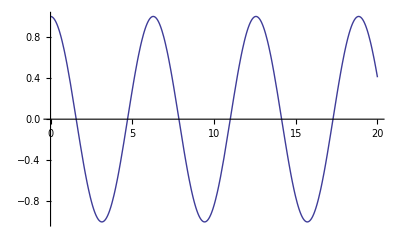
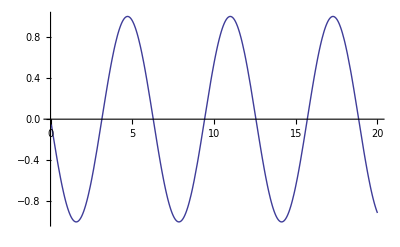
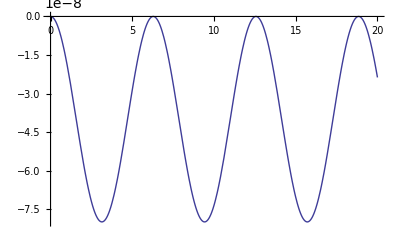
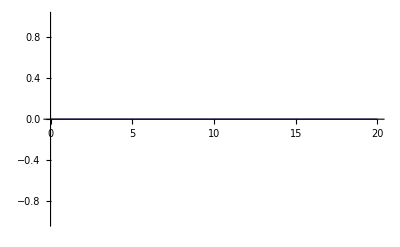
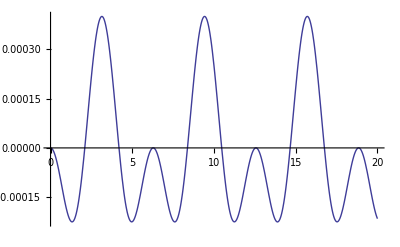
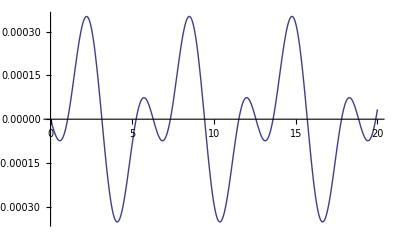
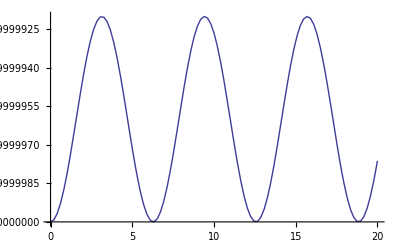
{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[Plot[s[n,m][t]/.ssolve,{t,0,20}],{n,1,3,1},{m,1,3,1}]
```

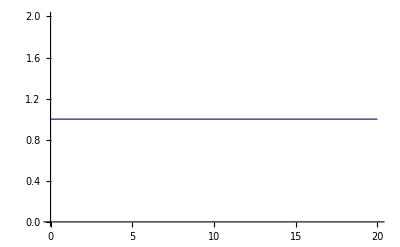
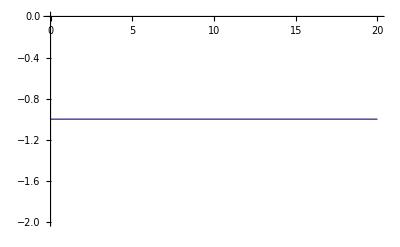
{{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
Table[Plot[2 ν[n,m][t]/.νsolve,{t,0,20}],{n,4,6,1},{m,3,3,1}]
```

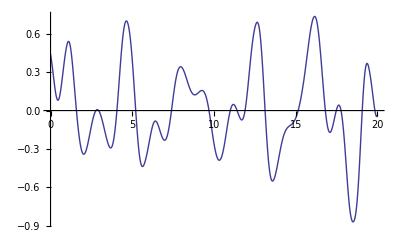
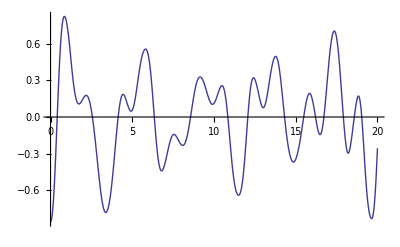
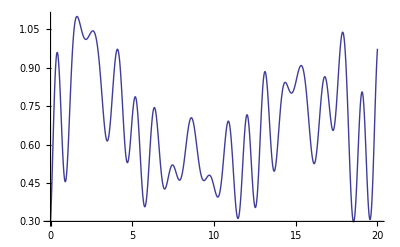
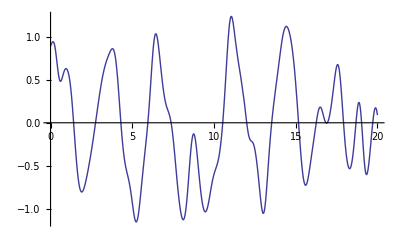
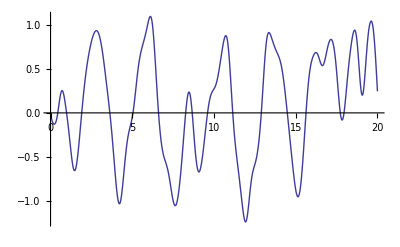
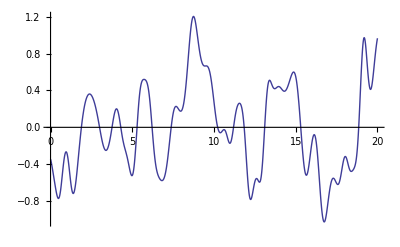
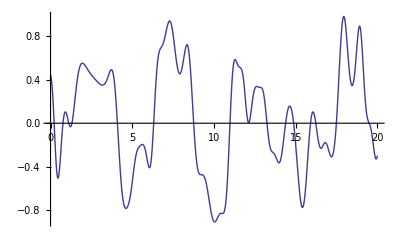
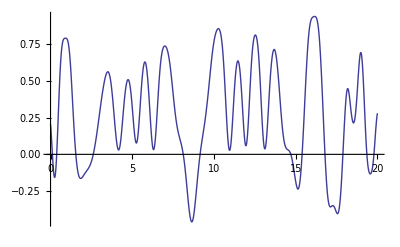

```mathematica
Table[Plot[ν[n,m][t]/.νsolve,{t,0,20}],{n,1,2,1},{m,1,8,1}]
```

```mathematica
Manipulate[Plot[ν[n,m][t]/.νsolve,{t,0,20}],{n,1,2,1},{m,1,8,1}]
```

## Gausian Wigner functions

```mathematica
meansz0={0,0,0,0,0,0,0,1/2 (1/(2 √3)+(√3)/2)};
```

```mathematica
varsz0={1/2,1/2,0,0,0,1/2,1/2,0};
```

```mathematica
meansxp1={1/2,0,0,1/4,0,0,0,1/2 (-1/(4 √3)+1/4 (1/(2 √3)-(√3)/2)+1/2 (1/(2 √3)+(√3)/2))};
varsxp1={0,1/(2 √2),1/(2 √2),1/4,1/(2 √2),1/(2 √2),1/2,√(-1/4 (-1/(4 √3)+1/4 (1/(2 √3)-(√3)/2)+1/2 (1/(2 √3)+(√3)/2))^2+1/4 (1/12+1/4 (1/(2 √3)-(√3)/2)^2+1/2 (1/(2 √3)+(√3)/2)^2))};
```

```mathematica
spindyn={};
Timing[
Do[
inits=Table[RandomVariate[NormalDistribution[meansxp1[[n]],√(varsxp1[[n]]+1/8)]],{Sites},{n,1,8}];
TWAres=
ParallelTable[
vν/.
NDSolve[
(eqnsν~Join~initialsν)/.{U->Uvalue,μ->μvalue,J->Jvalue,navg->navgvalue}~Join~Flatten[Table[Subscript[ν, 0][m,n]->inits[[m,n]],{m,1,Sites},{n,1,8}]],Flatten[vν],{t,0,tmax},MaxSteps->∞
],
{ii,mSIM}
];
spindyn=spindyn~Join~(Table[TWAres[[All,1,All,All]],{t,ts}]ᵀ)
,{j,0,(Runs/mSIM-1)}
]
]
```

{20.74731,Null}

```mathematica
avgspins=Total[spindyn]/Runs;
```

```mathematica
Dimensions[spindyn]
```

{1000,128,2,8}

```mathematica
Dimensions[avgspins]
```

{128,2,8}

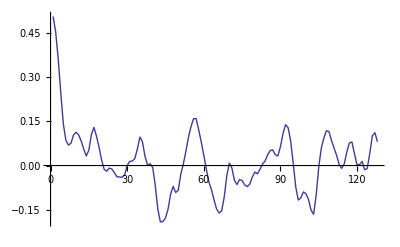

```mathematica
ListPlot[avgspins[[All,2,1]],Joined->True]
```

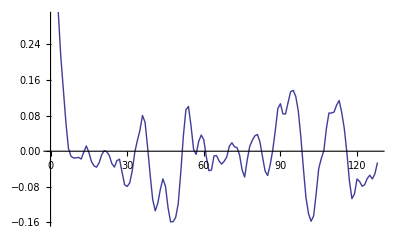

```mathematica
ListPlot[avgspins[[All,1,1]],Joined->True]
```

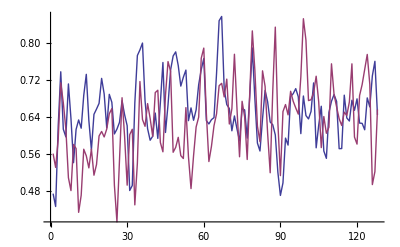

```mathematica
ListPlot[Table[2/3(1-√3 avgspins[[All,n,8]]),{n,1,2}],Joined->True]
```

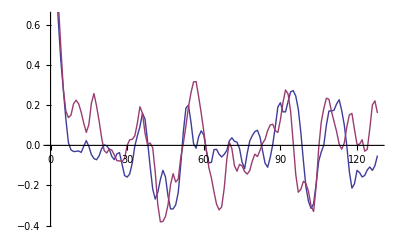

```mathematica
ListPlot[Table[2avgspins[[All,n,1]],{n,1,Sites}],Joined->True]
```

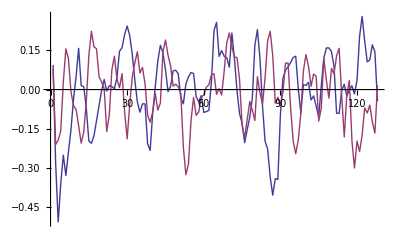

```mathematica
ListPlot[Table[2avgspins[[All,n,5]],{n,1,Sites}],Joined->True]
```

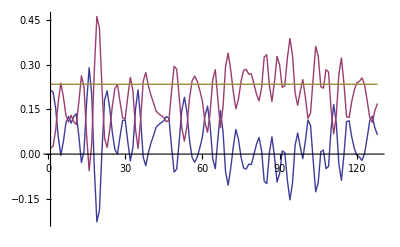

```mathematica
ListPlot[Table[2avgspins[[All,n,3]],{n,1,Sites}]~Join~{Sum[2avgspins[[All,n,3]],{n,1,Sites}]},Joined->True,PlotRange->All]
```

## Wigner with neg prob

```mathematica
svarsingreek={1/2 (β Conjugate[α]+α Conjugate[β]),1/2 (-ⅈ β Conjugate[α]+ⅈ α Conjugate[β]),1/2 (α Conjugate[α]-β Conjugate[β])};
```

```mathematica
Norm1=(4-√ⅇ)/(√ⅇ);
```

```mathematica
Norm2=ⅇ^(-1-1/(√2)) (4 (2+√2)+4 (-2+√2) ⅇ^(√2)+ⅇ^(1+1/(√2)));
```

```mathematica
Fock1Mag=ProbabilityDistribution[4 a ⅇ^(-2 a^2)Abs[(4 a^2-1)]/Norm1,{a,0,∞}];
```

```mathematica
Fock2Mag=ProbabilityDistribution[4 a ⅇ^(-2 a^2)Abs[(1-8 a^2+8 a^4)]/Norm2,{a,0,∞}];
```

```mathematica
randmag1=RandomVariate[Fock1Mag,{2,Sites,Runs}];
```

```mathematica
randmag2=RandomVariate[Fock2Mag,{Sites,Runs}];
```

```mathematica
metric1=1-2UnitStep[1/2-randmag1];
```

```mathematica
metric2=1-2UnitStep[randmag2-(√(2-√2))/2]*UnitStep[(√(2+√2))/2-randmag2];
```

```mathematica
randphase=RandomReal[{0,2π},{2,Sites,Runs}];
```

```mathematica
randrest=Table[RandomVariate[NormalDistribution[0,1/2]]+I RandomVariate[NormalDistribution[0,1/2]],{Sites},{Runs}];
```

```mathematica
randupinit[n_]:={randmag2[[n]] ⅇ^(ⅈ randphase[[1,n]]),randrest[[n]]};
randmiinit[n_]:={randmag1[[1,n]] ⅇ^(ⅈ randphase[[1,n]]),randmag1[[2,n]] ⅇ^(ⅈ randphase[[2,n]])};
randdoinit[n_]:={randrest[[n]],randmag2[[n]] ⅇ^(ⅈ randphase[[1,n]])};
```

```mathematica
randinits={randupinit[1],randmiinit[2],randdoinit[3],randupinit[4],randmiinit[5],randdoinit[6]};
```

```mathematica
Dimensions[randinits]
```

{6,2,100000}

```mathematica
randinits[[4,2,323]]
```

0.125475+0.226565 ⅈ

```mathematica
ResNorm=Norm2^4 Norm1^4;
```

```mathematica
ProgressIndicator[Dynamic[j],{0,(Runs/mSIM-1)}]
```

```mathematica
spindyn=Table[0,{Nt},{Sites},{3}];
runsdone=0;
Timing[
Do[
TWAres=ParallelTable[
Product[metric1[[n,m,mSIM j+ii]],{n,1,2},{m,{2,5}}]Product[metric2[[m,mSIM j+ii]],{m,{1,3,4,6}}]vs/.NDSolve[(eqnss~Join~initialss)/.{U->Uvalue,μ->μvalue,J->Jvalue,navg->navgvalue}~Join~Flatten[Table[Subscript[s, 0][m,n]->(svarsingreek[[n]]/.{α->randinits[[m,1,mSIM j+ii]],β->randinits[[m,2,mSIM j+ii]]}),{m,1,Sites},{n,1,3}]],Flatten[vs],{t,0,tmax},MaxSteps->∞
],
{ii,mSIM}
];
spindyn=spindyn+Total[Table[TWAres[[All,1,All]],{t,ts}]ᵀ];
runsdone=runsdone+1;
,{j,0,(Runs/mSIM-1)}
]
]
avgspins=ResNorm Re[spindyn]/Runs;
```

{3336.58,Null}

```mathematica
avgspins>>su2dw6uj1001m
```

```mathematica
Dimensions[avgspins]
```

{128,6,3}

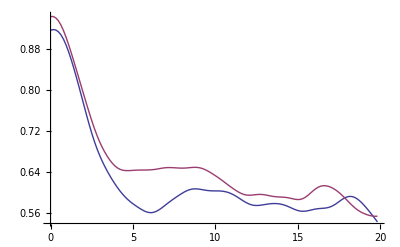

```mathematica
ListPlot[{{times,avgspins[[All,1,3]]}ᵀ,{times,avgspins[[All,4,3]]}ᵀ},Joined->True,PlotRange->All]
```

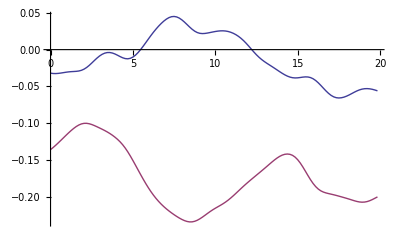

```mathematica
ListPlot[{{times,avgspins[[All,2,3]]}ᵀ,{times,avgspins[[All,5,3]]}ᵀ},Joined->True,PlotRange->All]
```

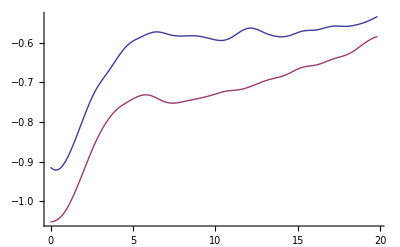

```mathematica
ListPlot[{{times,avgspins[[All,3,3]]}ᵀ,{times,avgspins[[All,6,3]]}ᵀ},Joined->True,PlotRange->All]
```